```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/implementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/implementation

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
qpData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,qpData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
momentumAvail= Normal[DeleteDuplicates[ds[Take,"momentum"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"momentum"->momentumAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_,invX_ :True]:=(
data=Apply[ds,directive];
x=(data[Take,keys[[1]]]//Normal);
y=(data[Take,keys[[2]]]//Normal);
If[invX,x=1/x];
result=Table[{x[[it]],y[[it]]},{it,Length[x]}];
Clear[x,y];
result
)
```

```mathematica
makeFits[data_,func_,arg_,points_]:=Table[Fit[d[[-Min[points,Length[d]];;-1]],func,arg],{d, data}]
```

```mathematica
getScaling[]:=(
fitFunctions={1,x,x^2};
fitPoints=4;

directive={Select[#coupling==J&&#momentum==k&&#interaction==B&]};
keys={"size","gap"};

fits={};
Do[(
Do[(
gap={};
Do[(
AppendTo[gap,extractData[scalingDataset,directive,keys]];
),{B,scalingAvail["interaction"]//Normal}];
AppendTo[fits,<|"coupling"->J,"momentum"->k,"fits"->makeFits[gap,fitFunctions, x,fitPoints]/.x->0|>];
),{k,scalingAvail["momentum"]//Normal}];
),{J,scalingAvail["coupling"]//Normal}];

Dataset[fits]
)
```

```mathematica
refineScaling[]:=(
scaling = scaling/.x->0;
scaling=Table[Table[Table[{beta[[bt]],scaling[[it,jt,bt]]},{bt,Length[beta]}],{jt,Length[scaling[[it]]]}],{it,Length[scaling]}];
)
```

```mathematica
getPlot[data_,scaling_,cutoff_]:=(
plt=ListPlot[data,
PlotRange->{{0,1.0},{-1.5,0.5}},ImageSize->Medium,
Frame->True,Axes->False,Joined->True,
FrameStyle->Directive[Black,20,FontFamily->"Bookman Old Style"],
PlotMarkers->{"●", 10},
PlotLegends->Placed[Table[StringJoin["L = ",ToString[NumberForm[L,{2,1}]]],{L,Select[qpAvail["size"],#>cutoff&]//Normal}],Right],
PlotLabel->Style[StringJoin["J = ",ToString[NumberForm[J,{2,1}]],"t   k = ",ToString[NumberForm[k,{2,1}]],"π"],Black,20,FontFamily->"Bookman Old Style"],
FrameLabel->{Style["β",Black,20,FontFamily->"Bookman Old Style"],Style["E_GS",Black,20,FontFamily->"Bookman Old Style"]},
LabelStyle->Directive[Black,12],
PlotStyle->Directive[Dashed]
];
splt=ListPlot[scaling,
PlotMarkers->{{"×",20},{"×",20}},
PlotStyle->Directive[Black]
];
Show[plt,PlotRangeClipping->False]
)
```

```mathematica
makePlotsGapB[cutoff_,scaling_]:=(

directive={Select[#coupling==J&&#momentum==k&&#size==L&]};
keys={"interaction","energy"};
beta={0.0,1.0};

plots={};
Do[(
Do[(
gap={};
Do[(
data=extractData[qpDataset,directive,keys,False];
If[Length[data]>0&&L>cutoff,AppendTo[gap,data]];
),{L,qpAvail["size"]//Normal}];
scdata=Table[{beta[[bt]],Normal[scaling[Select[#coupling==J&&#momentum==k&],"fits"]][[1,bt]]},{bt,Length[beta]}];
AppendTo[plots,getPlot[gap,scdata,cutoff]];
),{k,qpAvail["momentum"]//Normal}];
),{J,qpAvail["coupling"]//Normal}];

plots
)
```

```mathematica
JRange={"0.4","0.5","0.6","0.8"};
tails={"12-4-28_0.0-1.0-1.0"};
scaling ={};
Do[(
scalingDataset=Dataset[getAssoc["qp",JRange,tail]];
scalingAvail=Dataset[getStruct[scalingDataset]];
AppendTo[scaling,getScaling[]];
),{tail,tails}]

tails={"20-4-28_0.0-0.1-1.0"};
BPlots={};
Do[(
cutoff=12;
qpDataset=Dataset[getAssoc["qp",JRange,tails[[it]]]];
qpAvail=Dataset[getStruct[qpDataset]];
Print[Style[StringJoin["ΔE: J ∈ ",ToString[JRange]," @ ", tails[[it]]],16]];
AppendTo[BPlots,makePlotsGapB[cutoff,scaling[[it]]]];
),{it,Length[tails]}]
```

ΔE: J ∈ {0.4, 0.5, 0.6, 0.8} @ 20-4-28_0.0-0.1-1.0

```mathematica
Dataset[scaling]
```

Dataset[<>]

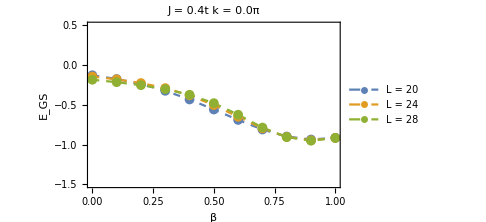
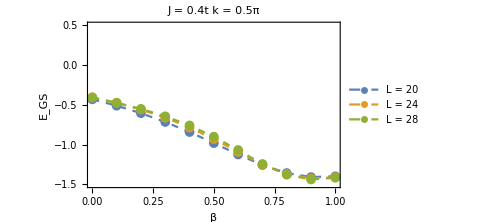
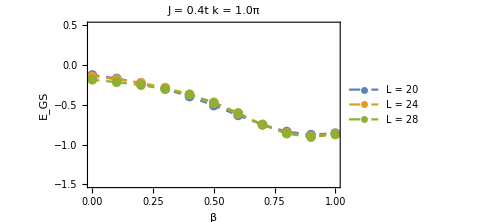
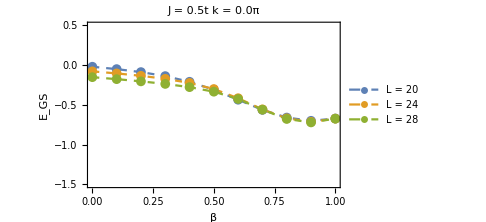
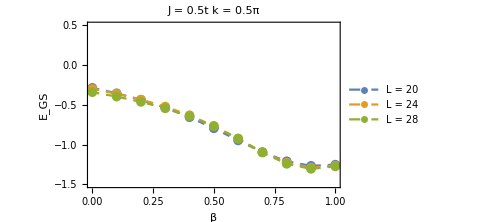
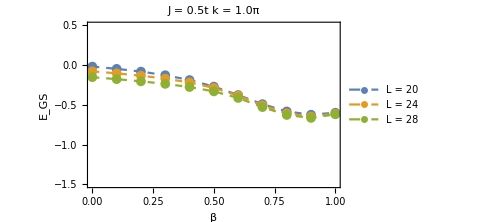
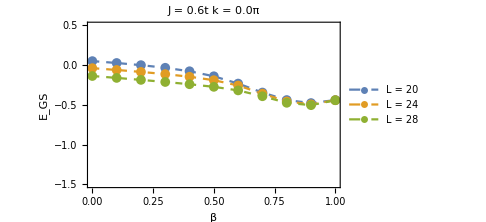
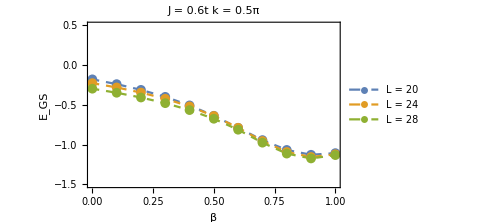
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Do[(
kDim=Length[DeleteDuplicates[scaling[[it]][Take,"momentum"]]];
plots=ArrayReshape[BPlots[[it]],{Length[BPlots[[it]]]/kDim,kDim}];
Print[Grid[plots]];
),{it,Length[BPlots]}]
```

```mathematica
SavePlots[]:=(
Do[(
Do[(
fileName=StringJoin["plots/ene/",
"ene_J=",ToString[qpAvail["coupling"][[iJ]]],
"_k=",ToString[qpAvail["momentum"][[ik]]],
".jpg"];
Export[fileName,BPlots[[1,(iJ-1)*Length[qpAvail["momentum"]//Normal]+ik]],ImageResolution->300];
),{ik,Length[qpAvail["momentum"]//Normal]}]
),{iJ,Length[qpAvail["coupling"]//Normal]}]
)
```

```mathematica
(*SavePlots[]*)
```